# Test Data Trace Plotting

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Tue 4 Mar 2014 13:01:11 )

( current Git HEAD:  c1b623a1c1f703ddee3ec7367c20c50915fc6ff2 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

## Load Data

```mathematica
testDataFileDirectory = ParentDirectory[NotebookDirectory[]]<>"\\_testFiles\\Neuralynx"
```

V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx

```mathematica
testFiles4=FileNames[testDataFileDirectory<>"\\Tet4*.ncs"]
```

{V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4a.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4b.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4c.ncs,V:\docs\bb\NounouM2\NounouM2\Testing\_testFiles\Neuralynx\Tet4d.ncs}

```mathematica
$NNReader@load[testFiles4]
```

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:4, dataAux ch:0, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeaderNull
     [dataORI ] XDataFilterHolder: XData: 4 ch, 3 seg, lengths=Vector(3339264, 123392, 6754816), fs=32000.0)     
          \ XDataFilterDecimate: factor=16     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: halfWindow=100
                    \ XDataFilterMinMaxAbs: halfWindow=100
                    \ XDataFilterFIR: kernel null (off)
     [dataAux ] XDataFilterHolder: XDataNull()
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

## NNTracePlot

```mathematica
tr=$NNReader@data[]@readTrace[0]
```

«JavaObject[breeze.linalg.DenseVector]»

```mathematica
$NNReader@dataFrameSegmentToMs[0,0]
```

0

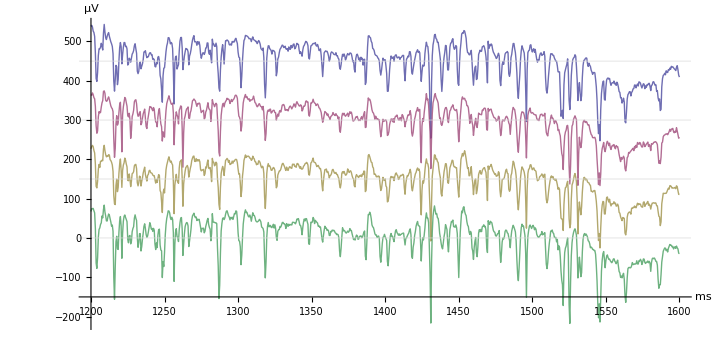

```mathematica
NNTracePlot[ Range[0,3], 1200 ;; 1600 , 0, NNStackLists->150]
```

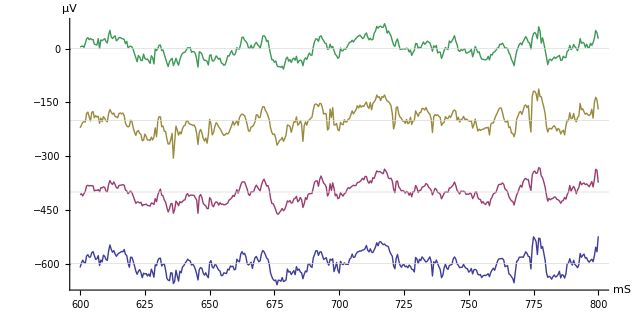

```mathematica
NNTracePlot[ Range[0,3], 600 ;; 800 , 0]
```